# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\All models comparison

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

### Ensemble of initial states ψ_s ⊗ ψ_e, Chaotic

# Wisniacki chain

## Chaotic

```mathematica
L=5;
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=50;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

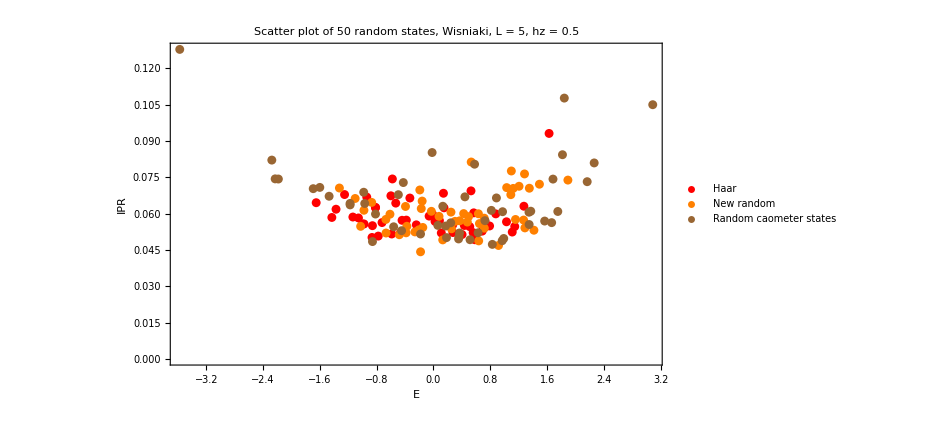

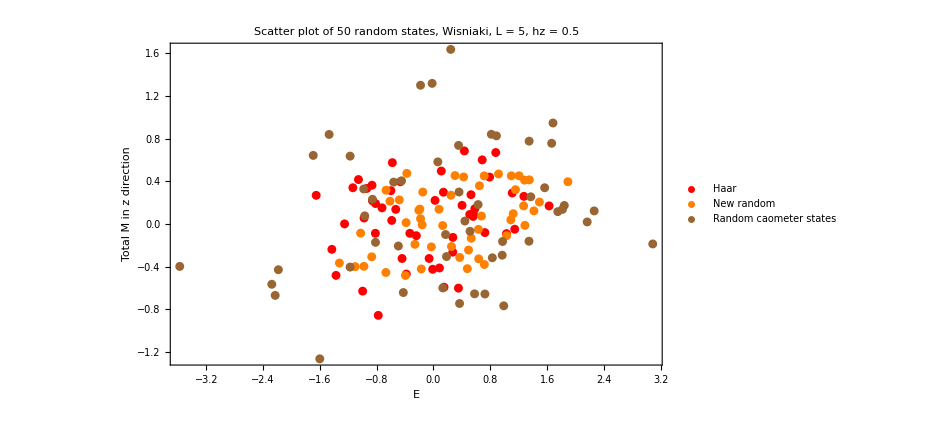

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

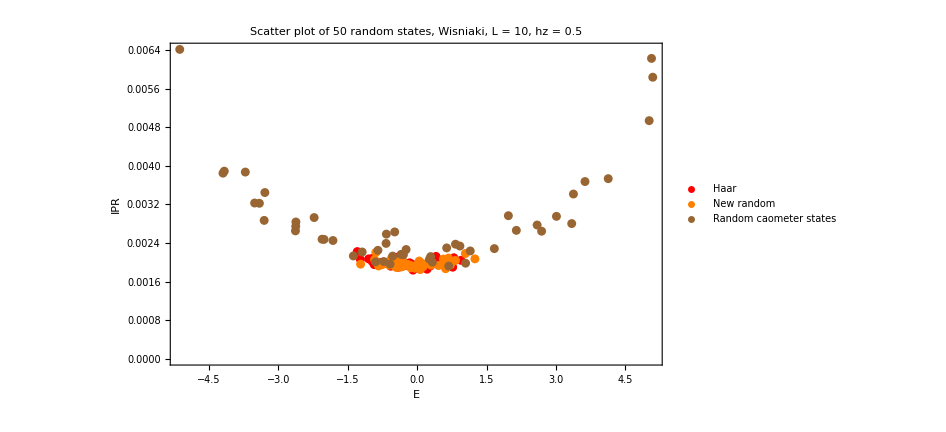

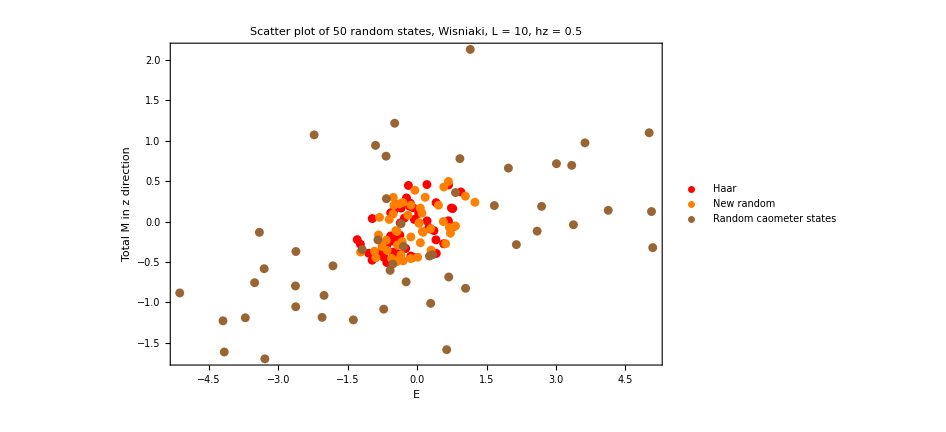

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
ψat=ParallelTable[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=ParallelTable[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=ParallelTable[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

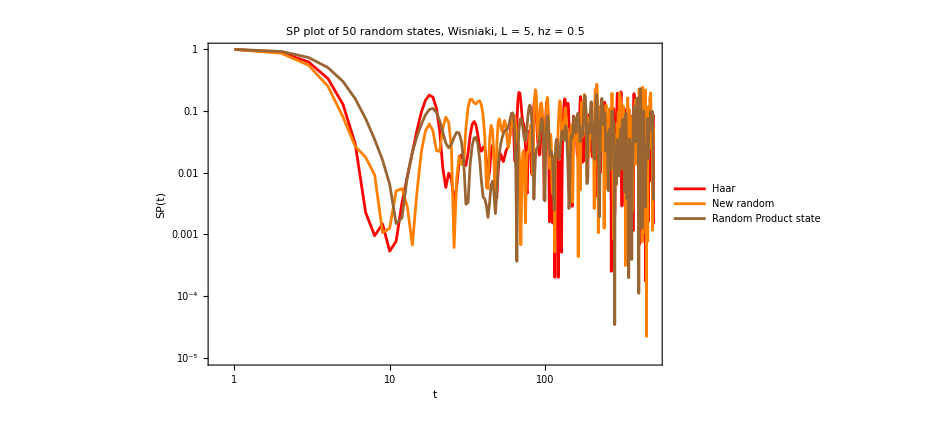

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

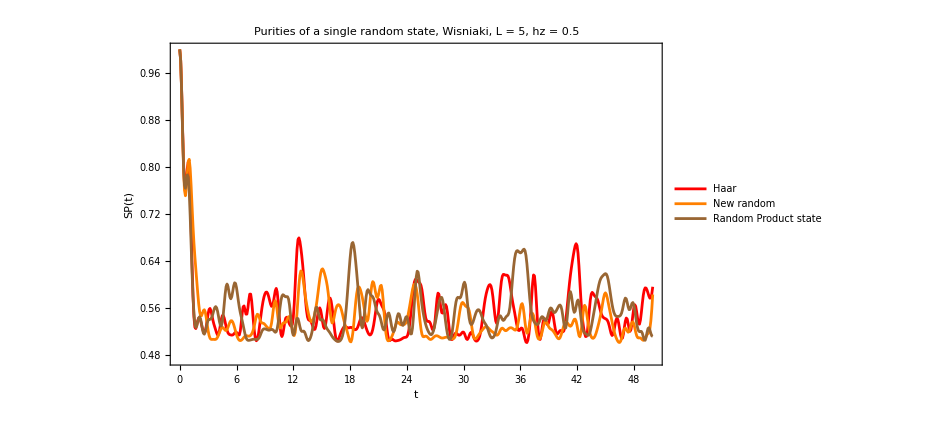

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reduceda//Dimensions
```

{501,2,2}

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
```

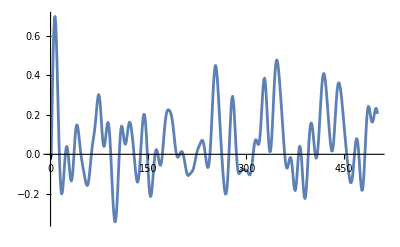

```mathematica
ListPlot[reducedmaga,Joined->True]
```

## Regular

```mathematica
L=8;
hx=J=1.;
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
caometer=Table[haar[1],{i,50}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

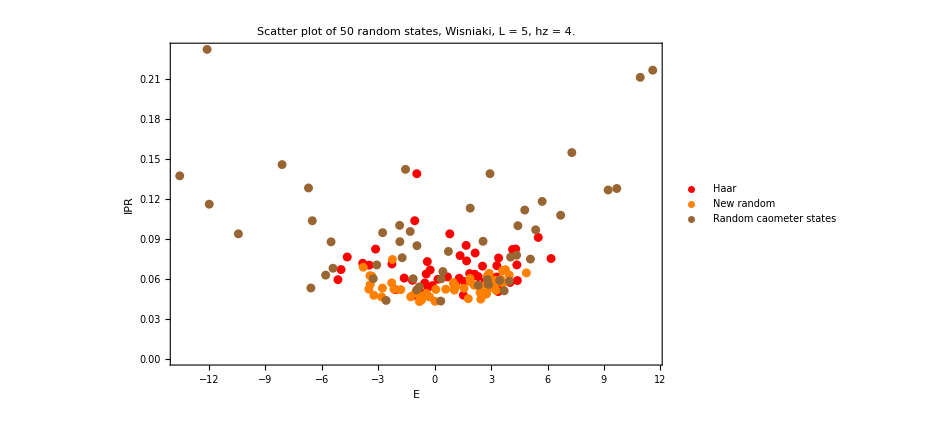

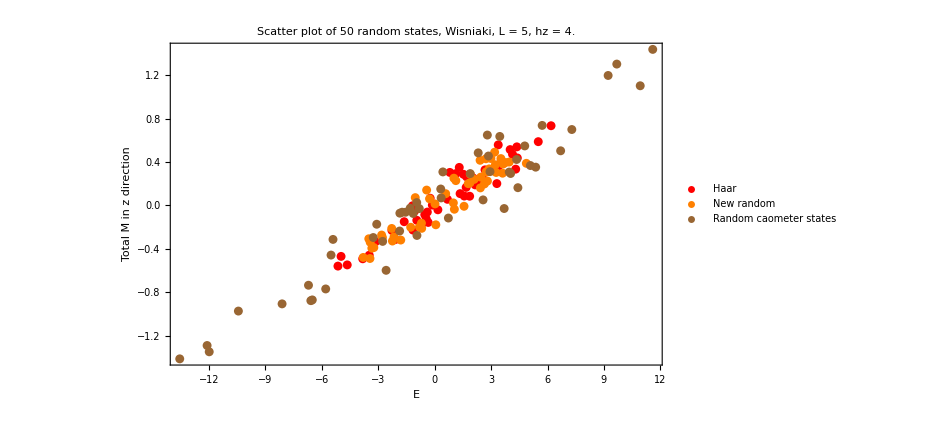

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

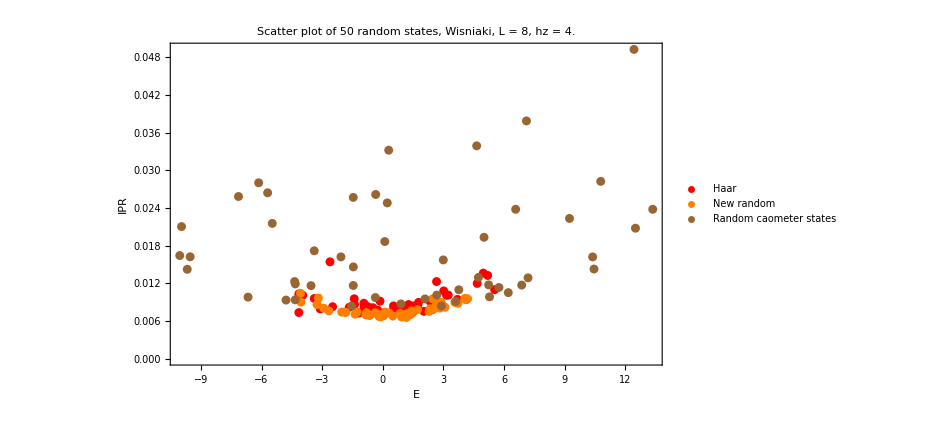

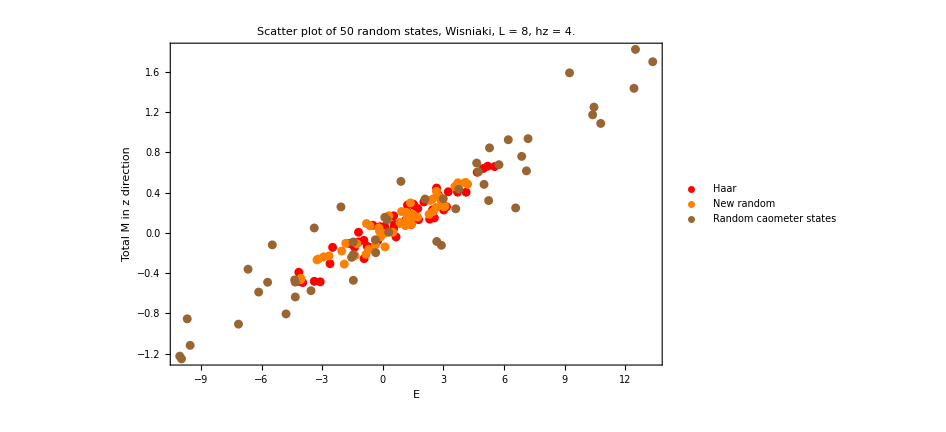

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

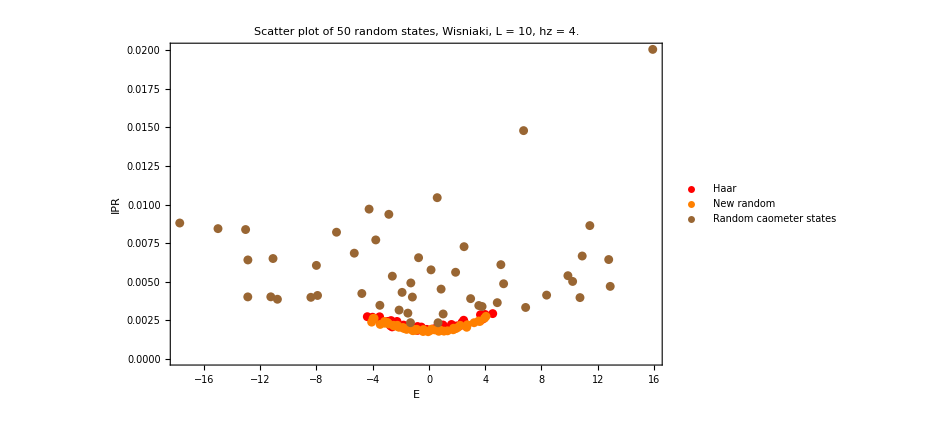

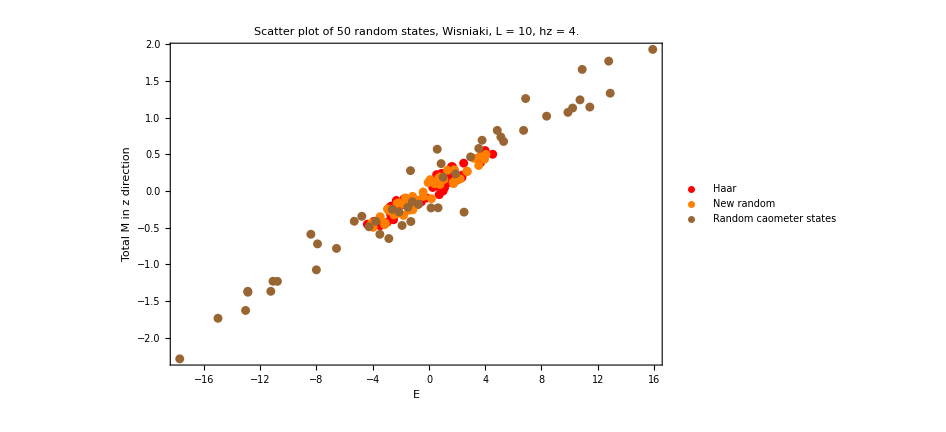

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
ψat=ParallelTable[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=ParallelTable[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=ParallelTable[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

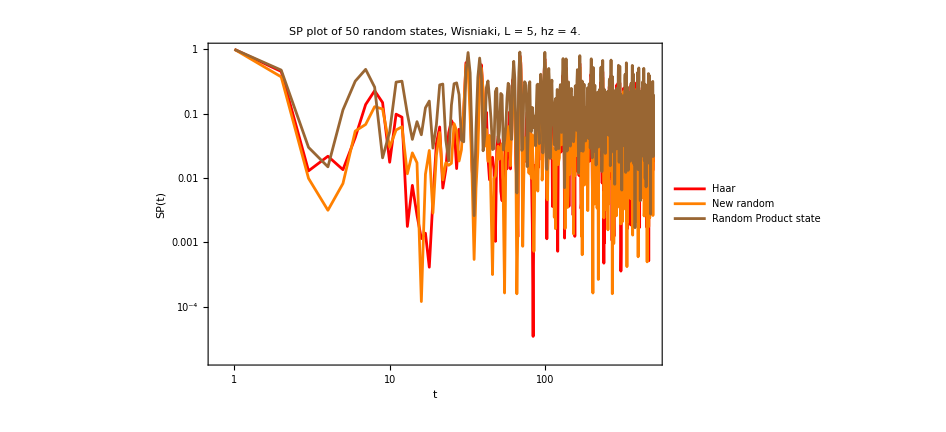

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

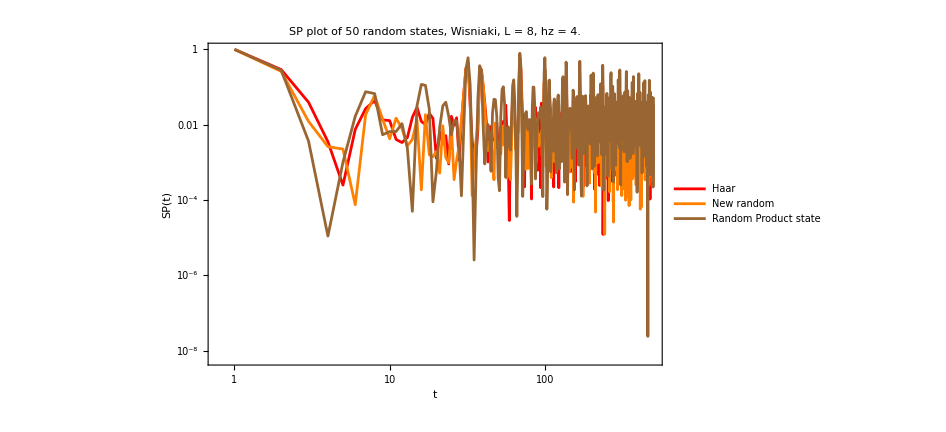

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

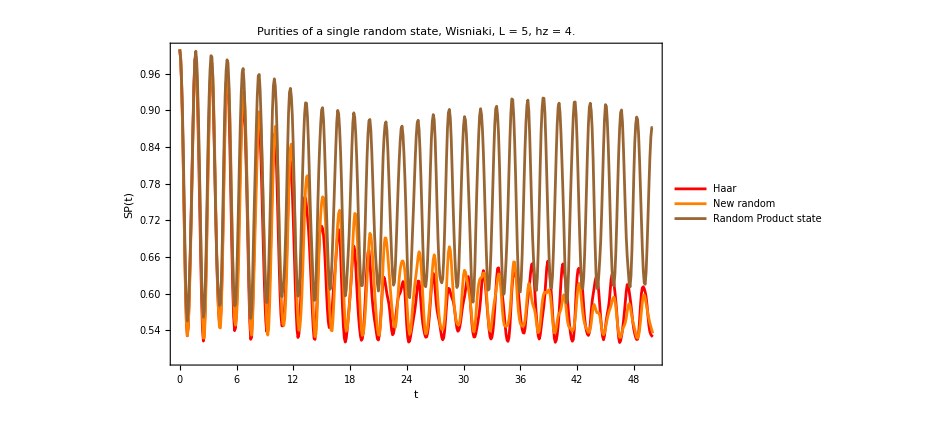

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

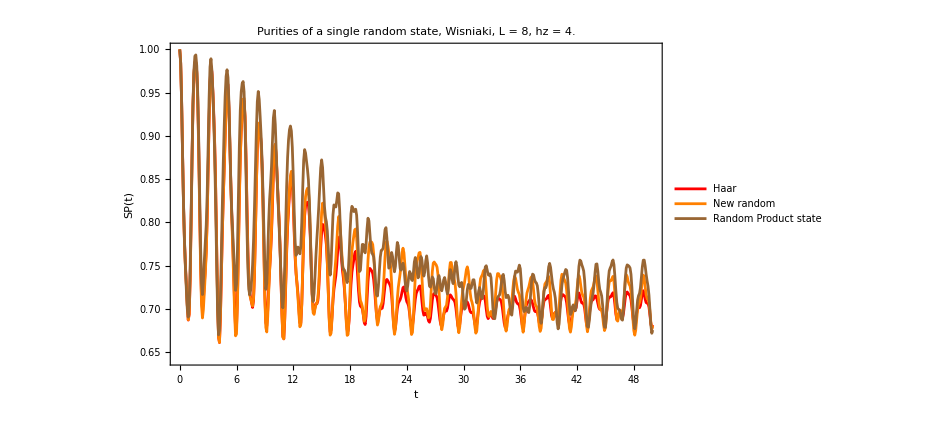

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

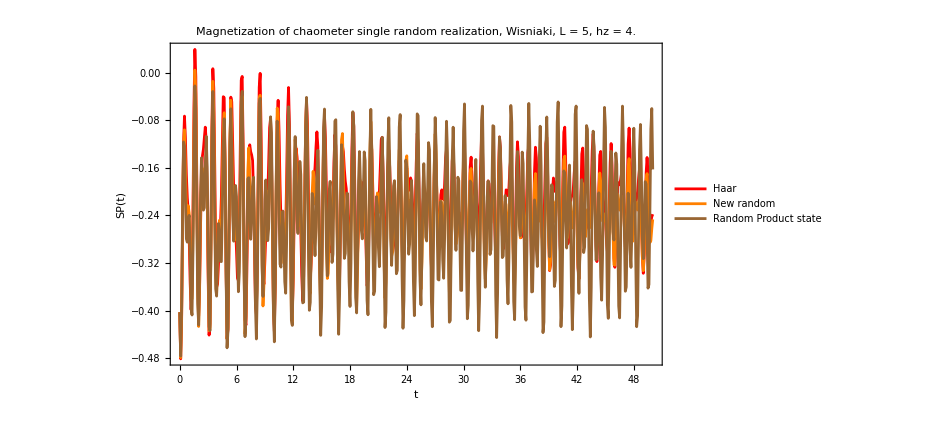

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

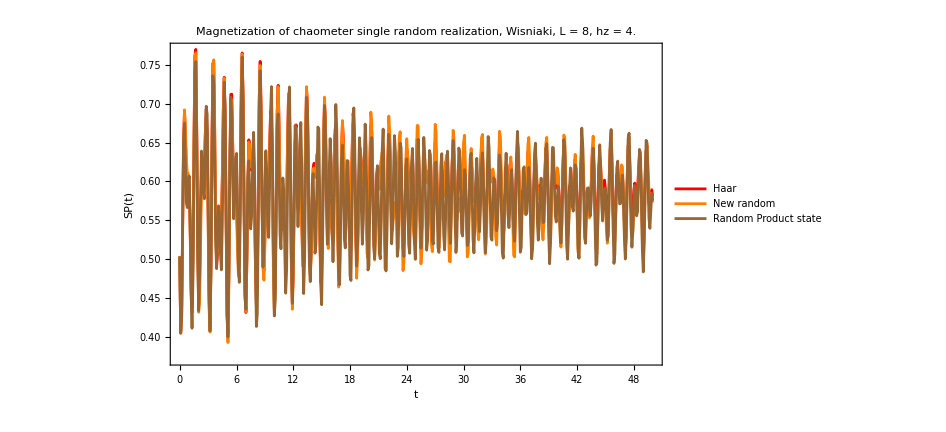

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

# XXZ Chain

```mathematica
L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=50;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

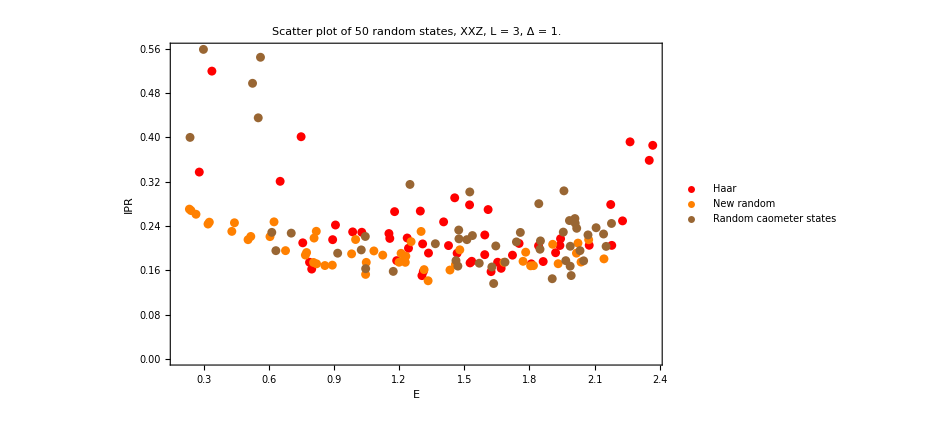

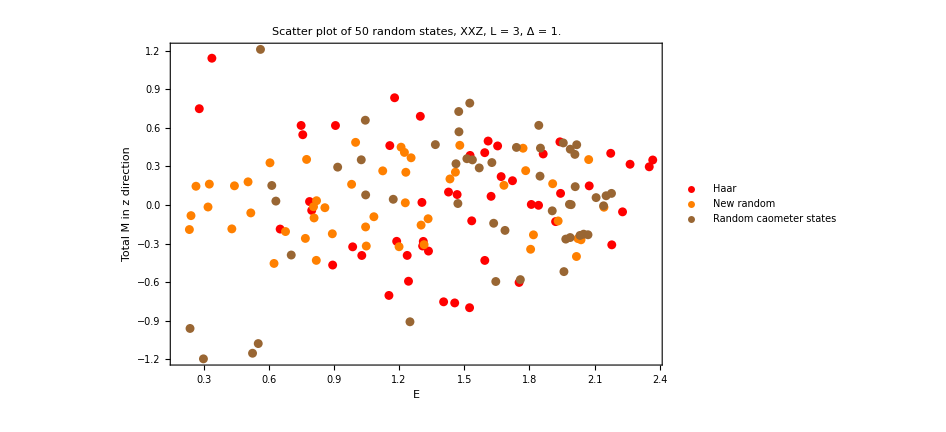

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

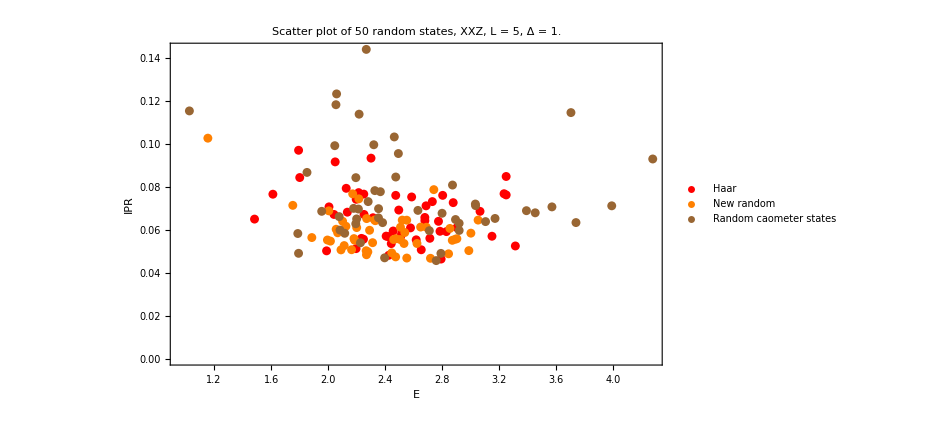

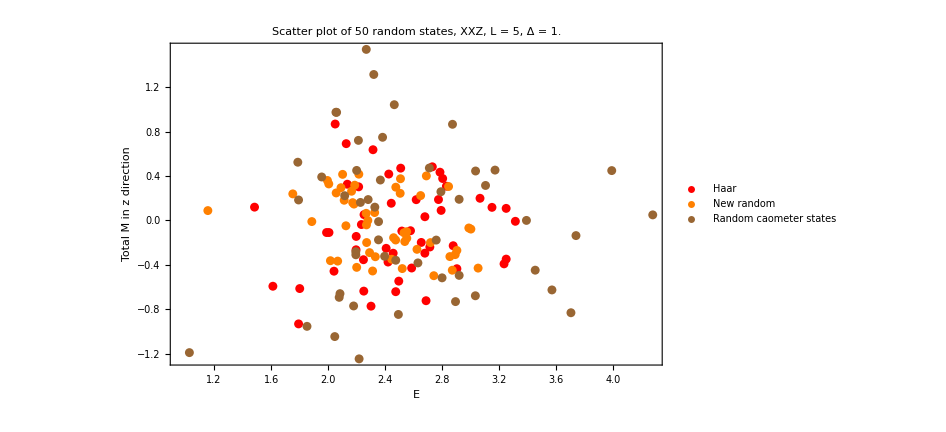

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

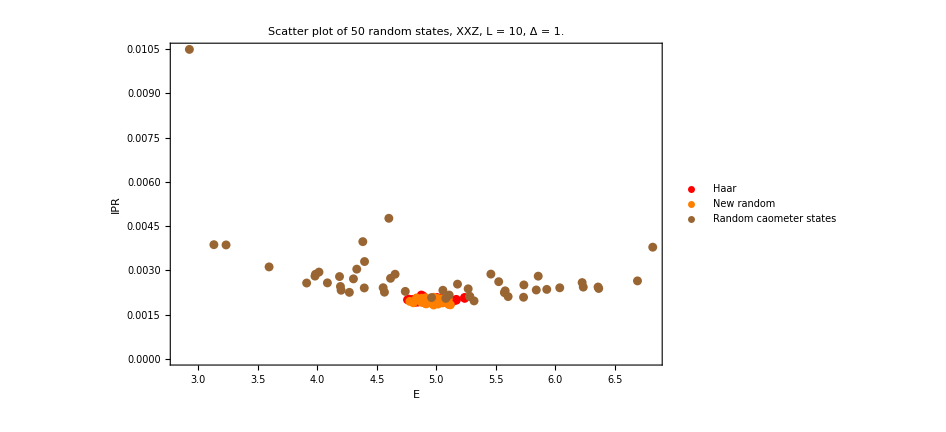

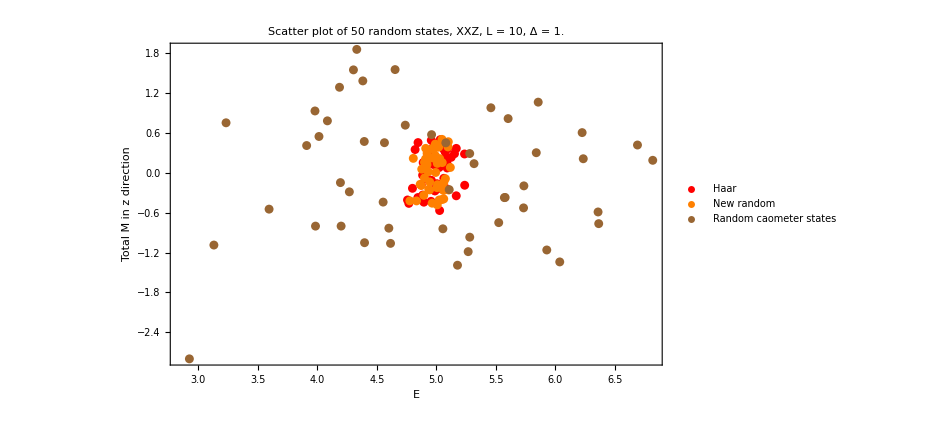

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

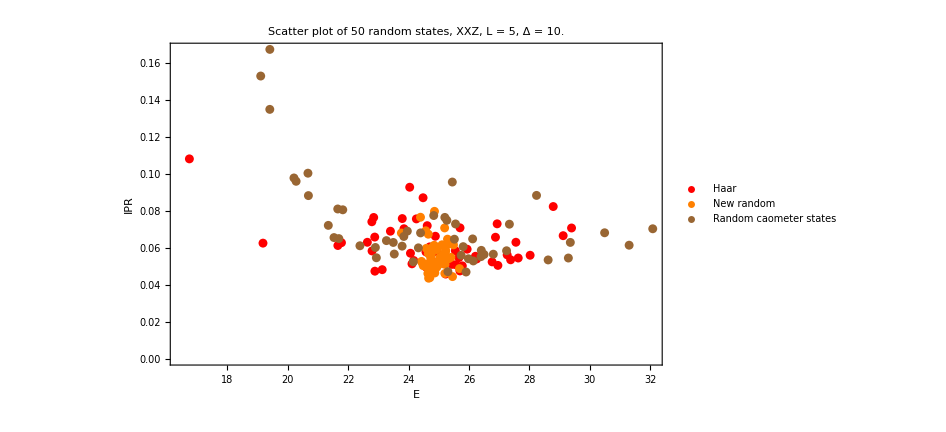

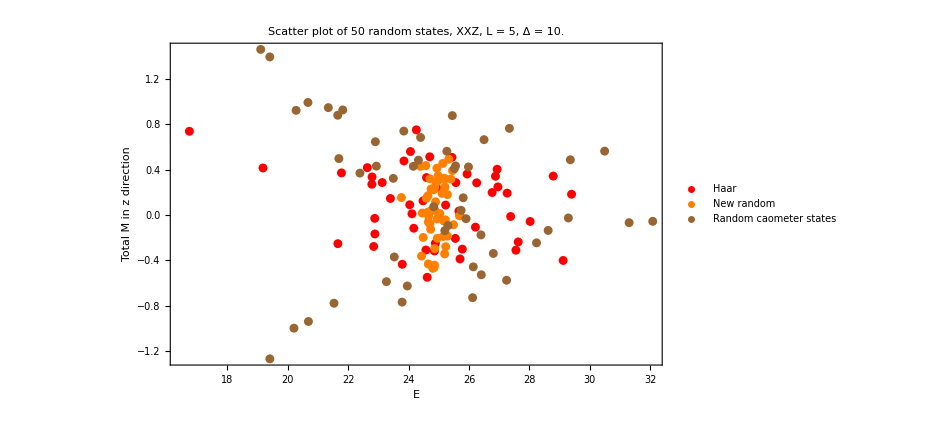

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

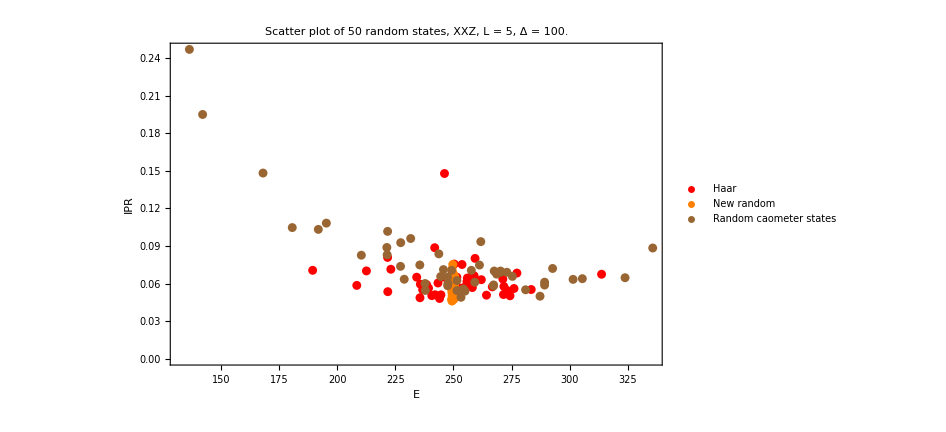

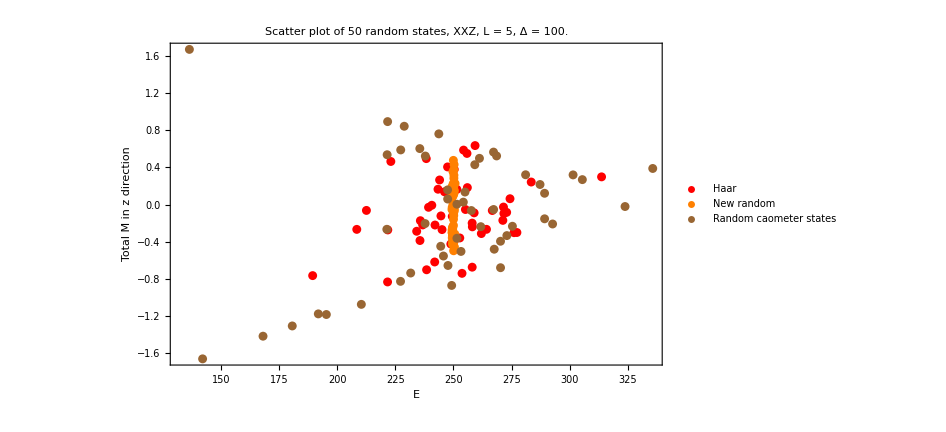

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

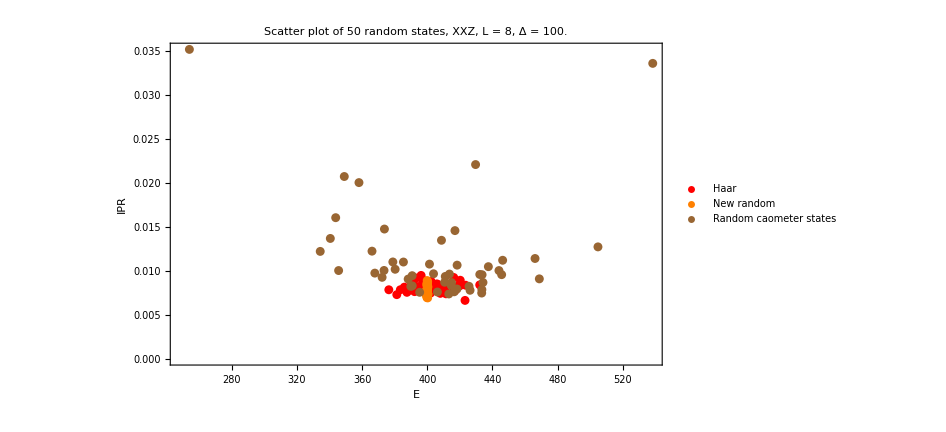

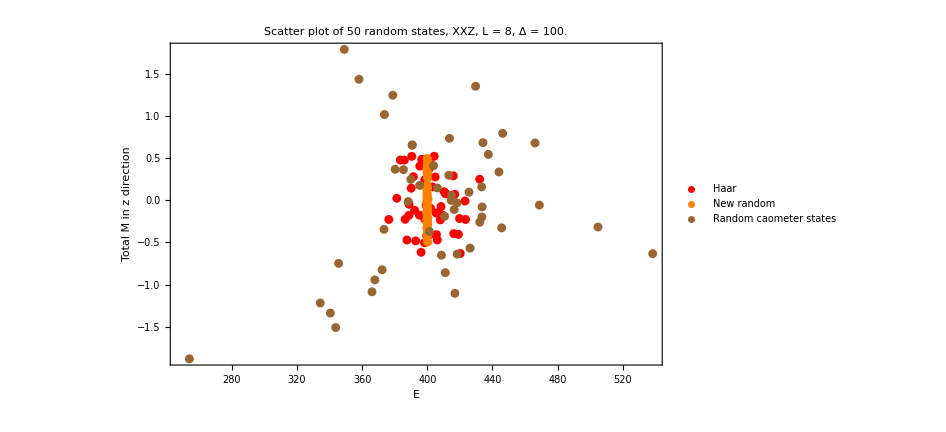

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
ψat=ParallelTable[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,10,0.1}];
ψbt=ParallelTable[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,10,0.1}];
ψct=ParallelTable[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,10,0.1}];
```

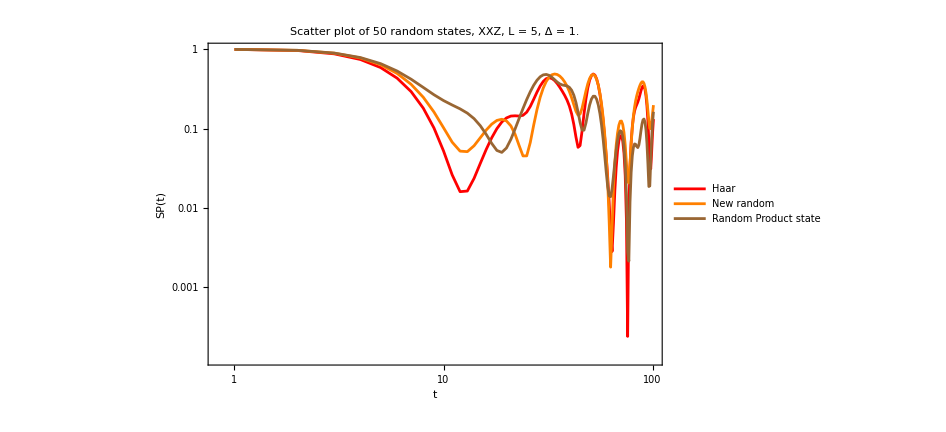

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

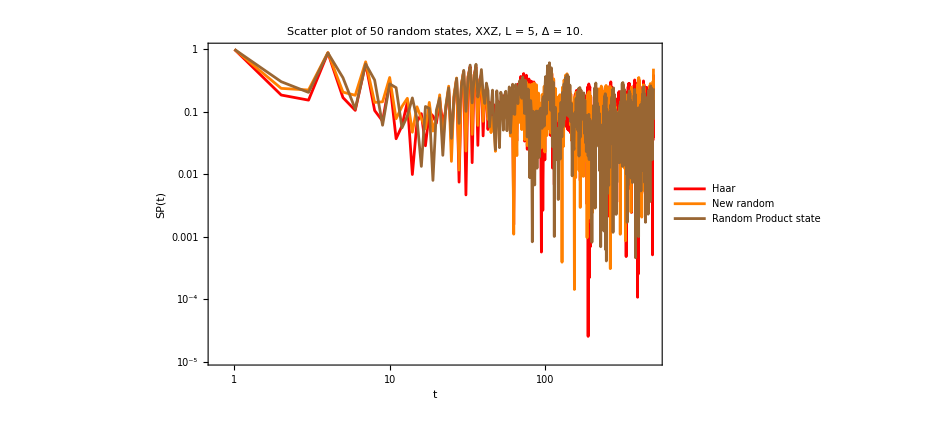

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

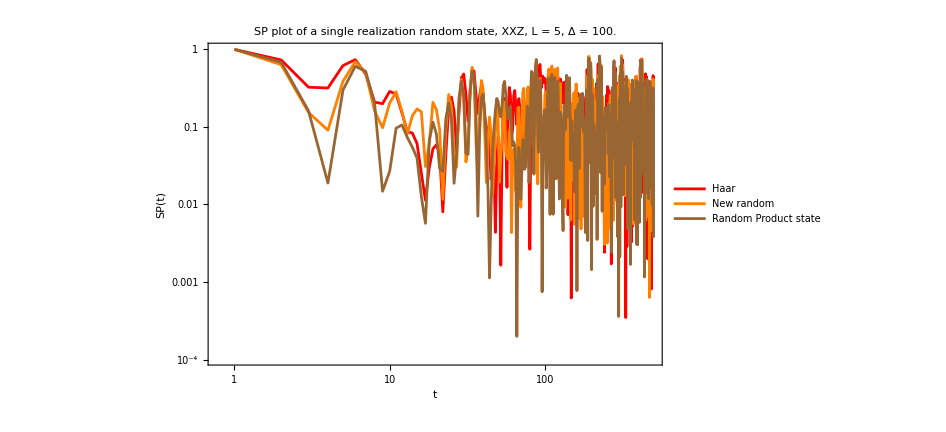

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of a single realization random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

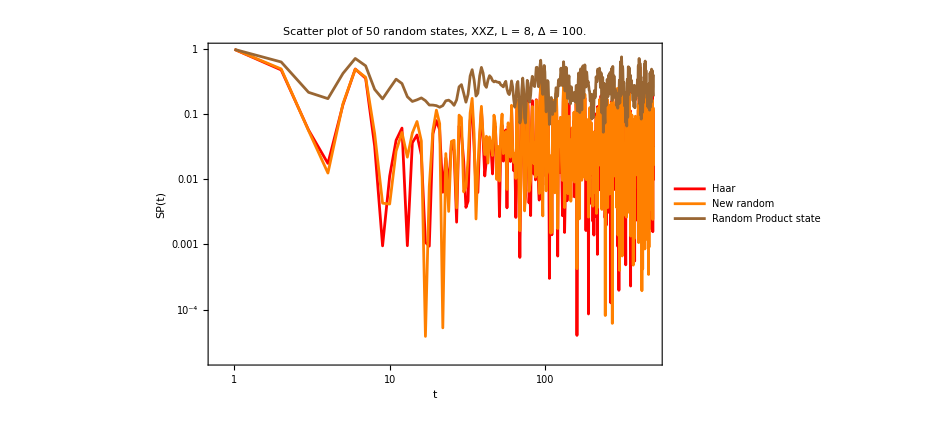

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,10,0.1];
```

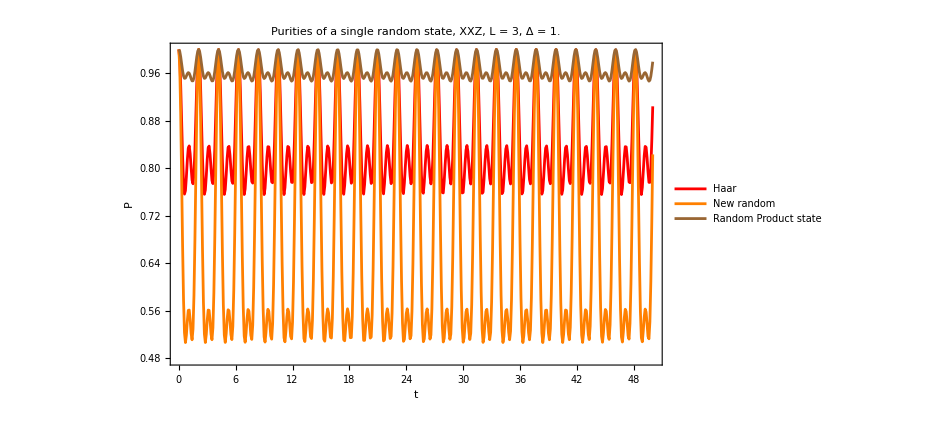

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

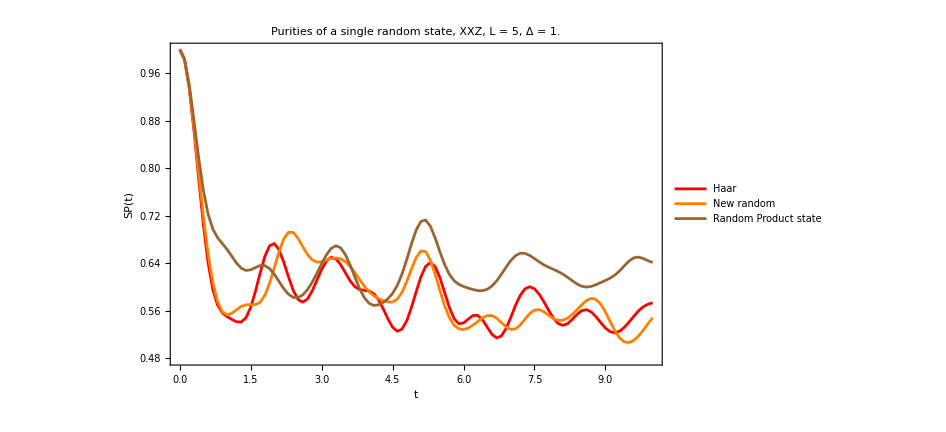

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

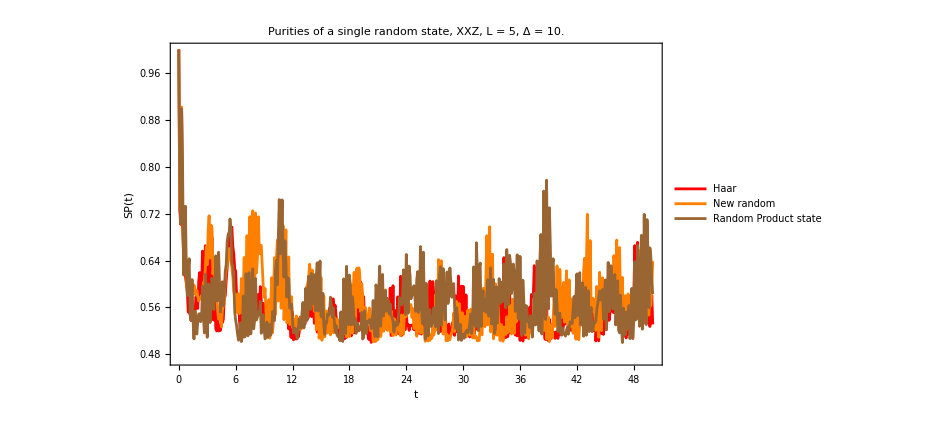

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

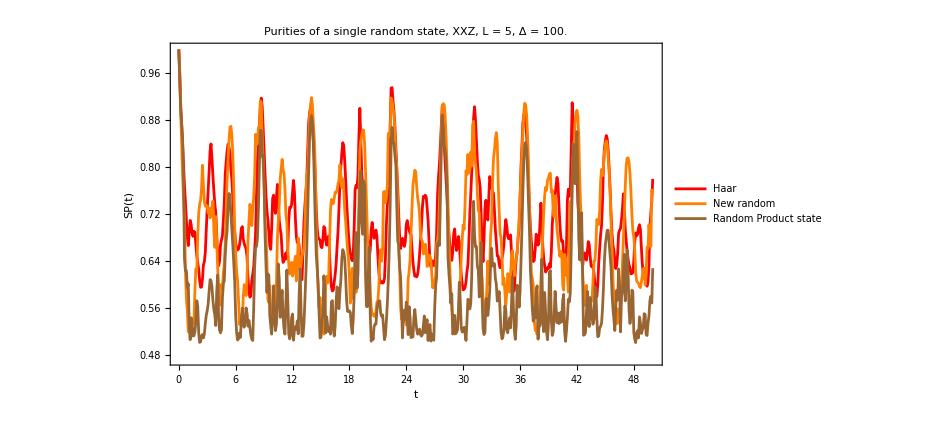

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

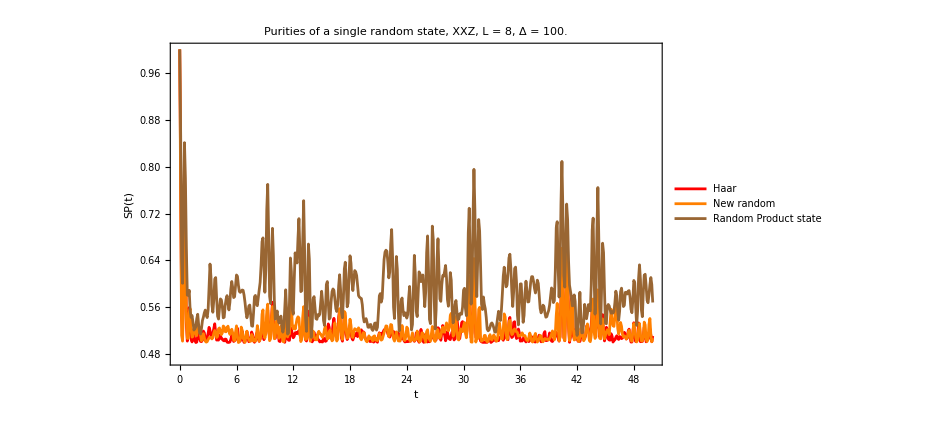

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

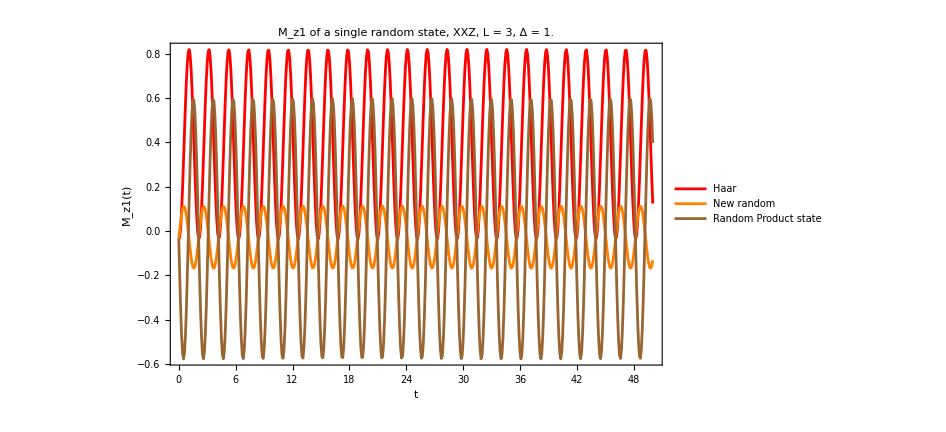

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

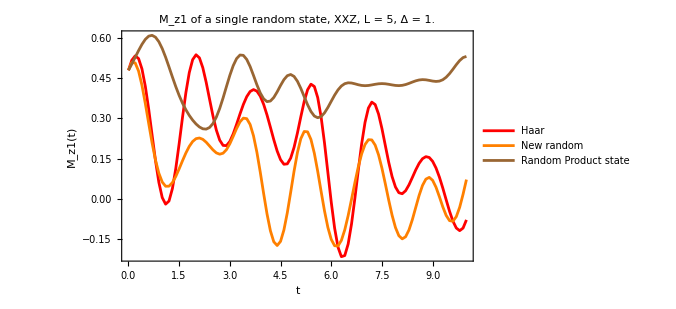

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->500,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

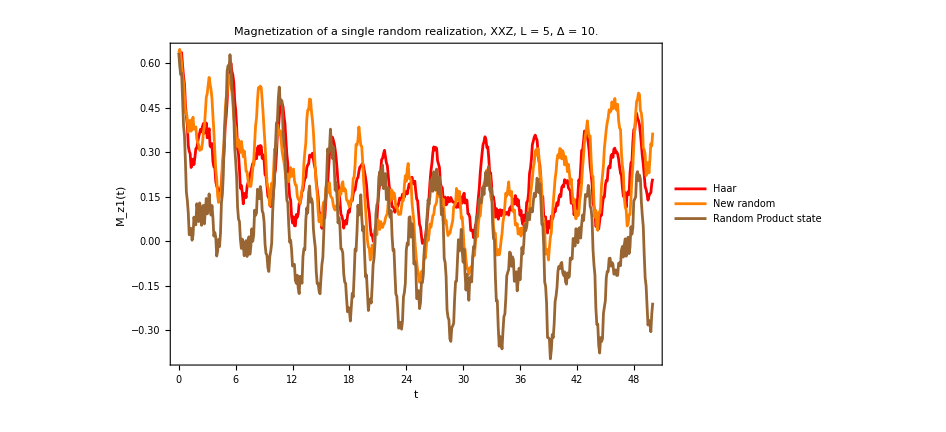

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of a single random realization, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

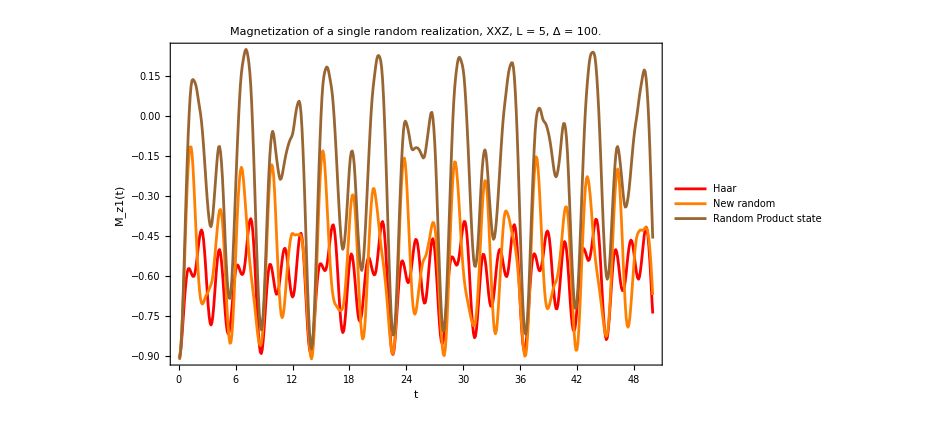

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of a single random realization, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

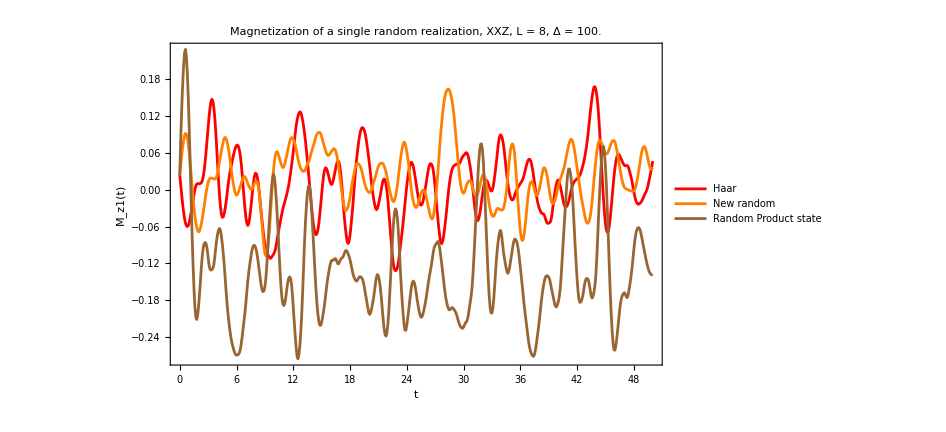

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of a single random realization, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

# LMG model

```mathematica
L=5;
α=-100.;
gx=0.43;
gy=0.57;
H=Hlmg[α,gx,gy,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
eigenvec=Orthogonalize[eigenvec];
```

```mathematica
ale=50;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

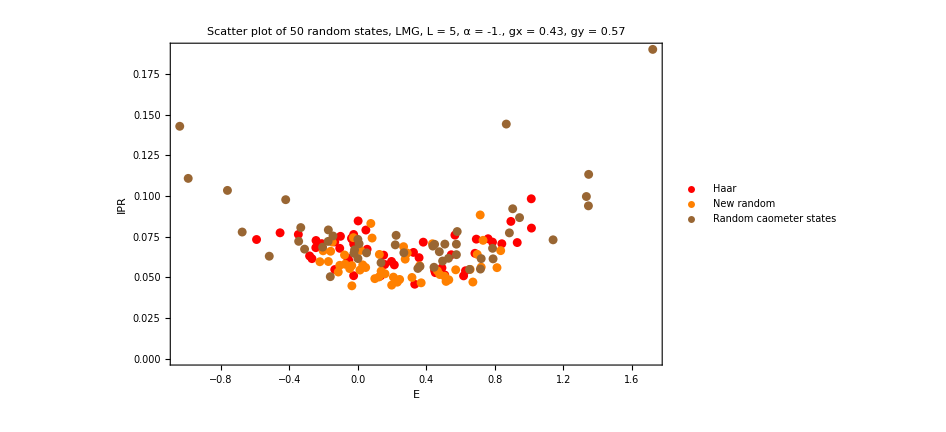

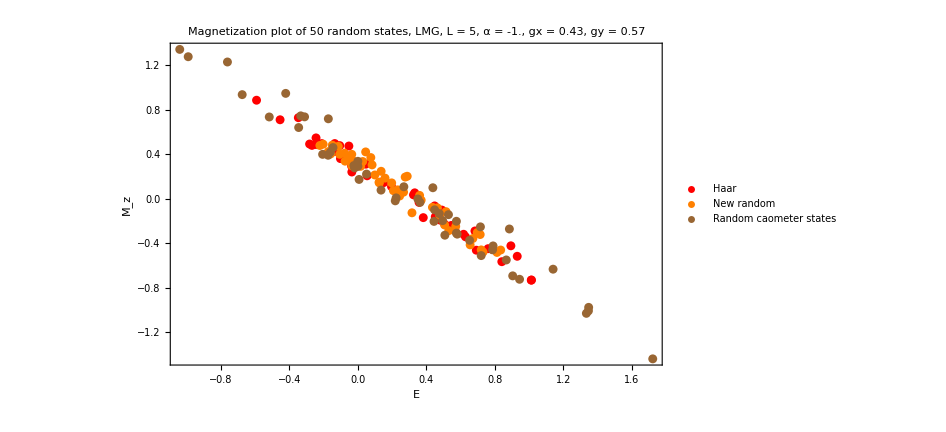

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Magnetization plot of "<>ToString[ale]<>" random states, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],17,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["M_z"]}]
```

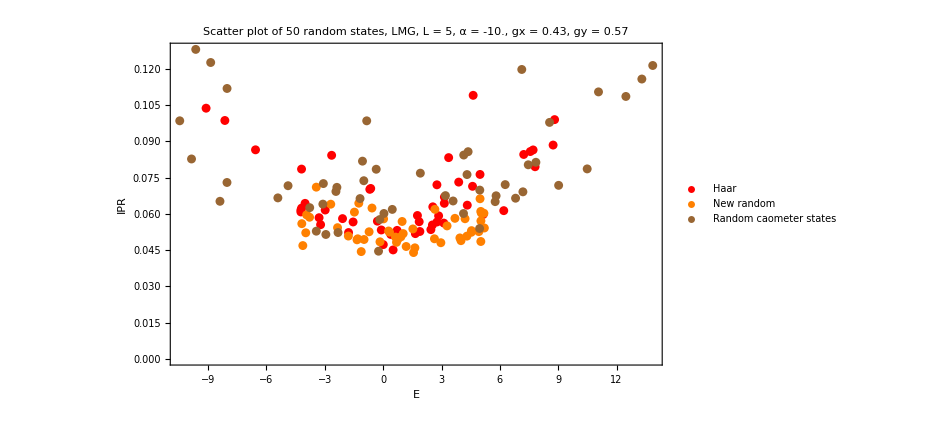

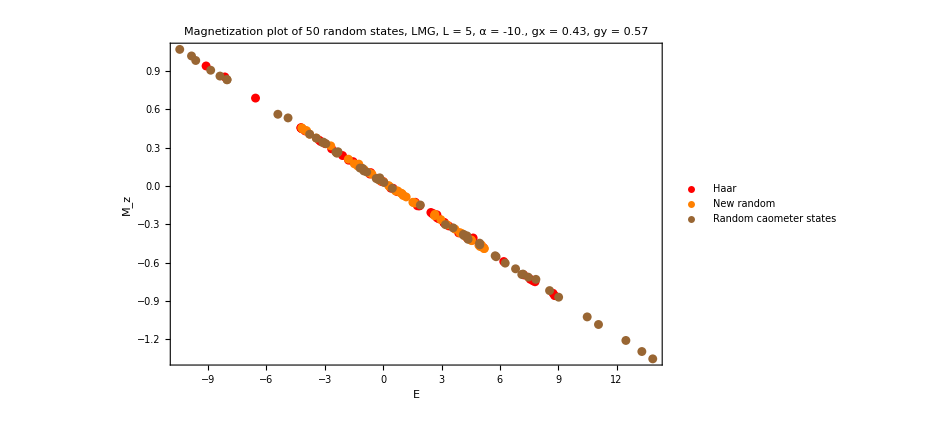

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Magnetization plot of "<>ToString[ale]<>" random states, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],17,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["M_z"]}]
```

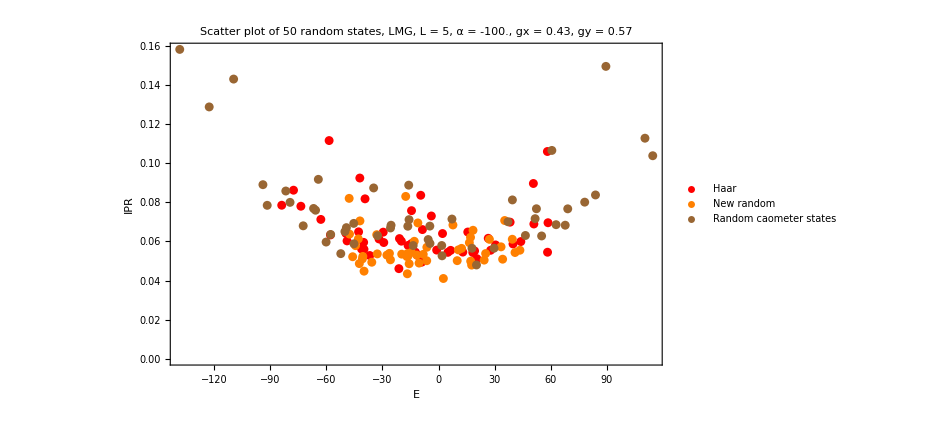

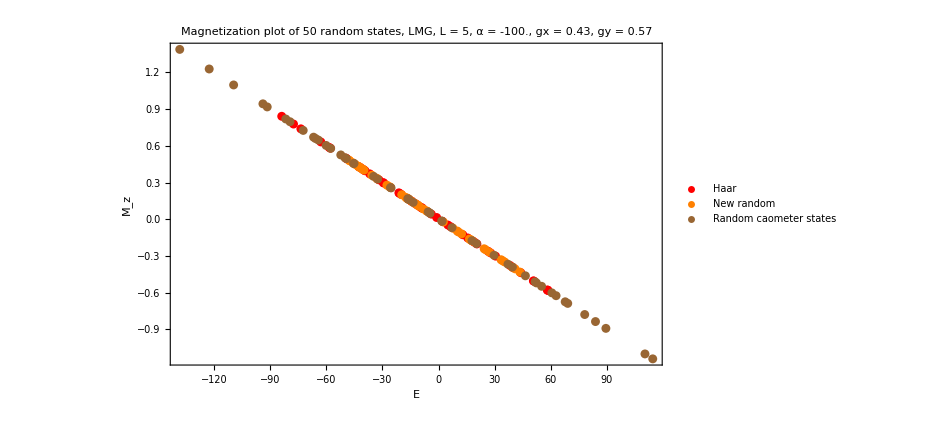

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Magnetization plot of "<>ToString[ale]<>" random states, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],17,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["M_z"]}]
```

```mathematica
ψat=ParallelTable[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,100,0.1}];
ψbt=ParallelTable[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,100,0.1}];
ψct=ParallelTable[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,100,0.1}];
```

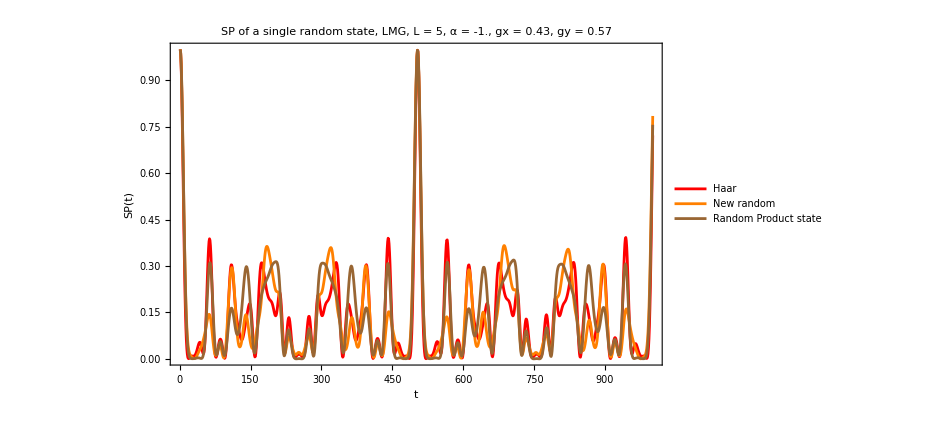

```mathematica
ListPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

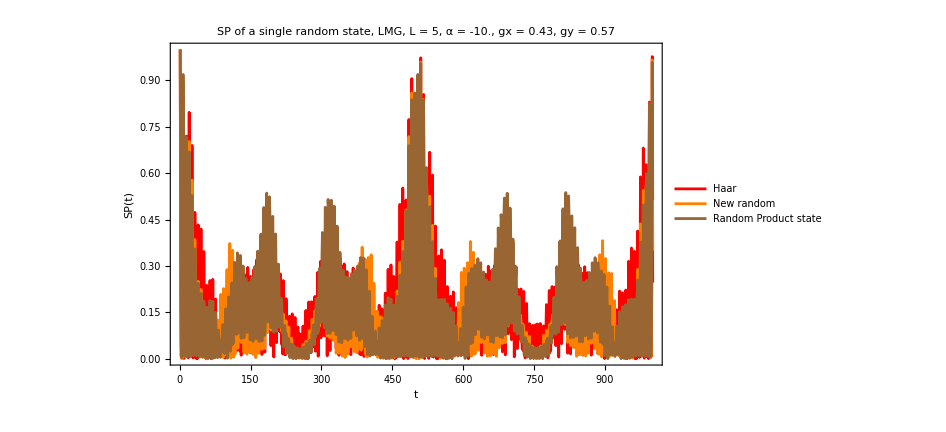

```mathematica
ListPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

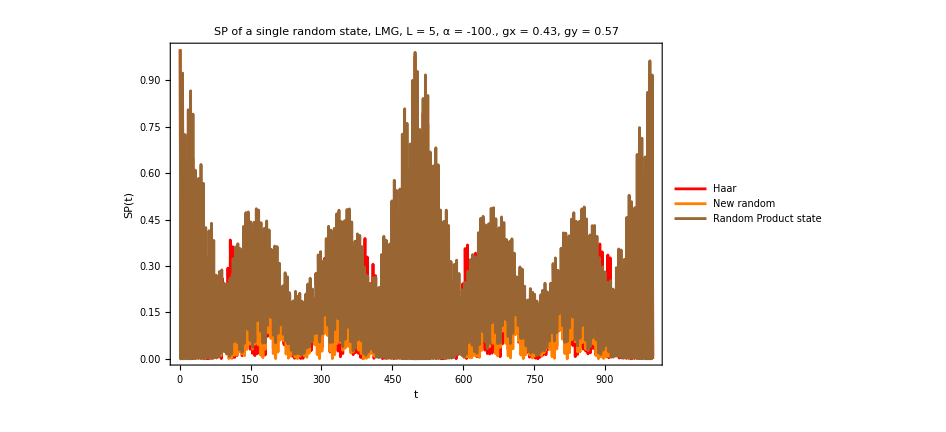

```mathematica
ListPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

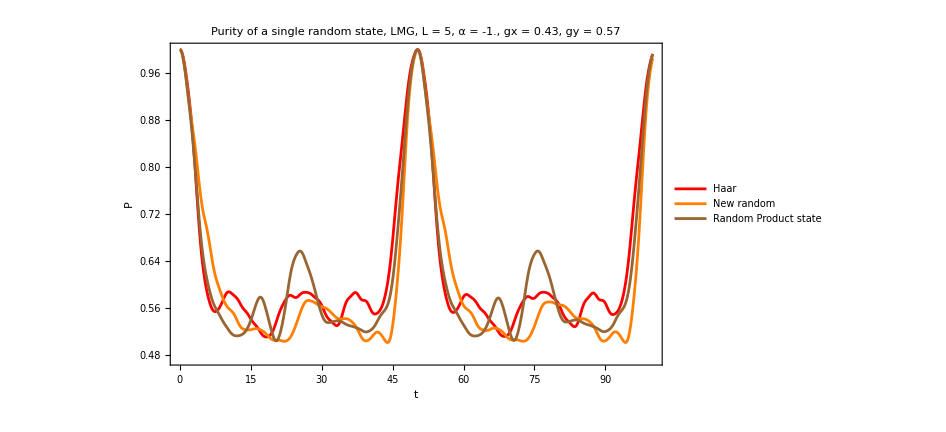

```mathematica
tlist=Range[0,100,0.1];
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purity of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

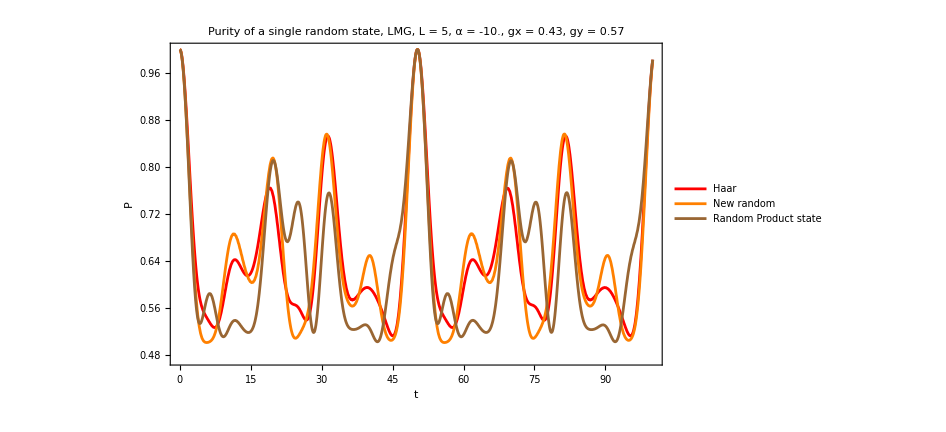

```mathematica
tlist=Range[0,100,0.1];
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purity of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

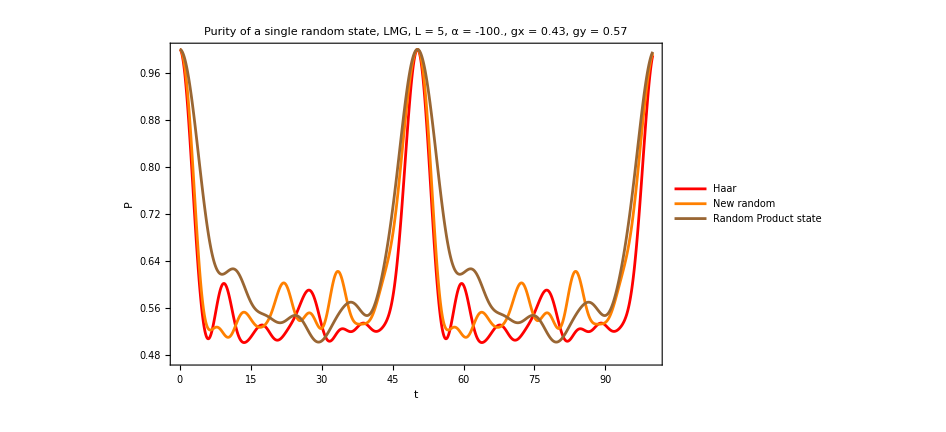

```mathematica
tlist=Range[0,100,0.1];
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purity of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

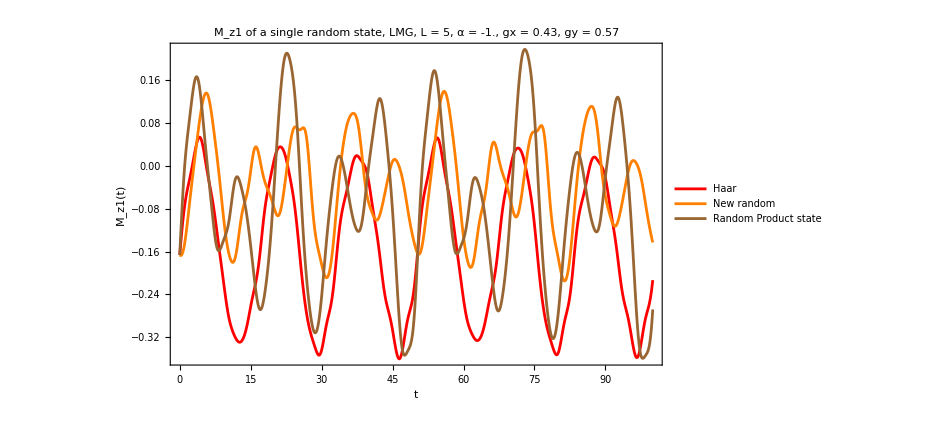

```mathematica
tlist=Range[0,100,0.1];
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

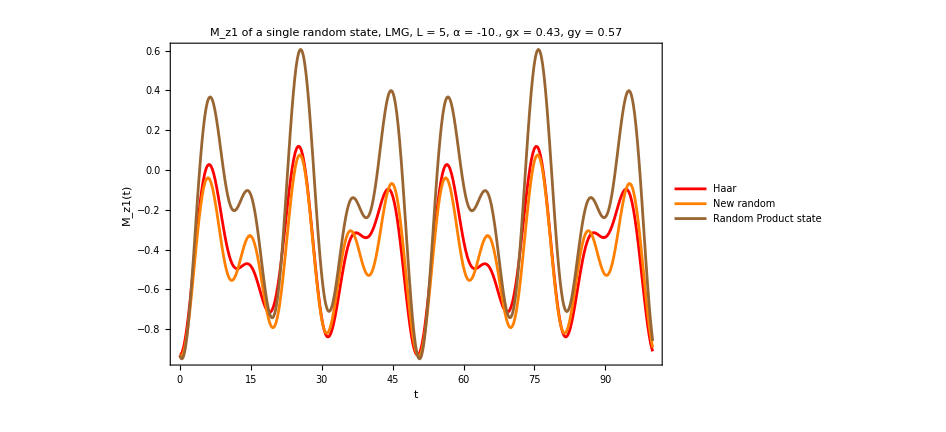

```mathematica
tlist=Range[0,100,0.1];
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

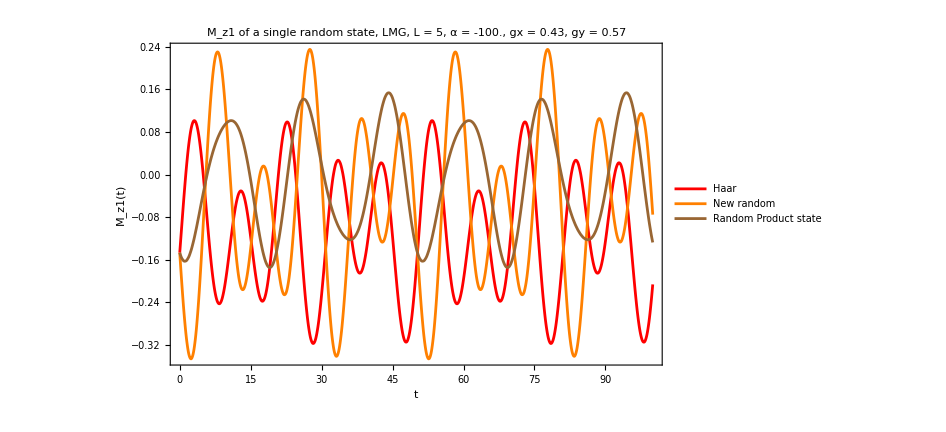

```mathematica
tlist=Range[0,100,0.1];
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```